# cutoffs - varying r

## fix σ; calculate <g|ρ|g> for ε = 10Ω; plot as a function of r, the time for which switching is constant

## parameters

```mathematica
α=1;
Ω=1;
ε=10 Ω;
```

```mathematica
numSteps=9;
rMin=0.2/Ω;rMax=2/Ω; rStepSize=Abs[rMin-rMax]/numSteps;
rValues=Table[r,{r,rMin,rMax,rStepSize}];
```

```mathematica
rValues
```

{0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.}

## smearing function

```mathematica
σ0=10^-4/Ω;
σ=σ0;
σNorm=σ/σ0;
```

```mathematica
f[x_]:=1/(σ*√π)ⅇ^(-x^2/σ^2)
ftil[k_]:=FourierTransform[f[x],x,k,FourierParameters->{1,-1},Assumptions->σ∈Reals&&σ>0]
```

## switching function

```mathematica
chiT1[t_,r_]:=1/(r+T)1/2*(1+Cos[π/r(t+T/2)])
chiT2[t_,r_]:=1/(r+T)
chiT3[t_,r_]:=1/(r+T)1/2*(1+Cos[π/r(t-T/2)])
```

## k integrand

### the first interval

```mathematica
tpInt1[t_?NumericQ,k_?NumericQ,r_?NumericQ]:=tpInt1[t,k,r]=NIntegrate[chiT1[tp,r]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2-r,t}]
```

```mathematica
tInt1[k_?NumericQ,r_?NumericQ]:=tInt1[k,r]=α*NIntegrate[chiT1[t,r] tpInt1[t,k,r],
{t,-T/2-r,-T/2}]
```

### the second interval

```mathematica
tpInt2[t_,k_,r_]:=Integrate[chiT2[tp,r]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,-T/2,t}]
```

```mathematica
tInt2[k_,r_]:=α*Integrate[chiT2[t,r] tpInt2[t,k,r],
{t,-T/2,T/2}]
```

### the third interval

```mathematica
tpInt3[t_?NumericQ,k_?NumericQ,r_?NumericQ]:=tpInt3[t,k,r]=NIntegrate[chiT3[tp,r]*Cos[k*(t-tp)]*Cos[Ω*(t-tp)],{tp,T,t}]
```

```mathematica
tInt3[k_?NumericQ,r_?NumericQ]:=tInt3[k,r]=α*NIntegrate[chiT3[t,r] tpInt3[t,k,r],
{t,T/2,T/2+r}]
```

this integrand with the transition from Abs[k] → k taken into account (i.e. can now properly integrate from 0 to ∞ with proper factor of 2)

```mathematica
kIntegrand[k_,r_]:=-1/π*k*ftil[k]^2*(tInt1[k,r]+tInt2[k,r]+tInt3[k,r])
```

## cutoff functions

```mathematica
gaussianCutoff[k_]:=ⅇ^((-Abs[k]^2)/(2 ε^2));
lorentzianCutoff[k_]:=ε^2/(Abs[k]^2+ε^2);
expCutoff[k_]:=ⅇ^((-Abs[k])/(2 ε));
sharpCutoff[k_]:=HeavisideTheta[k+ε,-k+ε];
```

## <g|ρ|g>

```mathematica
T=0.5;
```

```mathematica
pGauss=Table[α+λ^2*NIntegrate[gaussianCutoff[k]*kIntegrand[k,r],{k,0,∞}],{r,rMin,rMax,rStepSize}]
```

```mathematica
pLor=Table[α+λ^2*NIntegrate[lorentzianCutoff[k]*kIntegrand[k,r],{k,0,∞}],{r,rMin,rMax,rStepSize}]
```

```mathematica
pSharp=Table[α+λ^2*NIntegrate[kIntegrand[k,r],{k,0,ε}],{r,rMin,rMax,rStepSize}]
```

```mathematica
pExp=Table[α+λ^2*NIntegrate[expCutoff[k]*kIntegrand[k,r],{k,0,∞}],{r,rMin,rMax,rStepSize}]
```

## plot

```mathematica
λ=0.1;Ω=.;
```

```mathematica
dataGauss=Transpose[{rValues,pGauss}];
dataLor=Transpose[{rValues,pLor}];
dataSharp=Transpose[{rValues,pSharp}];
dataExp=Transpose[{rValues,pExp}];
```

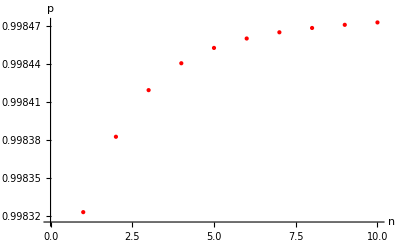

```mathematica
ListPlot[{dataGauss,dataLor,dataSharp,dataExp},
AxesLabel->{r Ω,p},
PlotStyle->{Red,Blue,Green,Black},
PlotMarkers->Automatic,
PlotLabel->Style["",FontSize->16]]
```

## save the data!!

```mathematica
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pGaussvr.csv",dataGauss];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pLorvr.csv",dataLor];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pSharpvr.csv",dataSharp];
Export["C:/Users/Public/Documents/emma/udw-detector-shape/Cutoffs/pExpvr.csv",dataExp];
```